```mathematica
(* Some helper functions *)
linearToSrgb[x_]:=If[x<0.0031308,12.92*x,(1+0.055)*Power[x,1/2.4]-0.055]
srgbToLinear[x_]:=If[x<0.04045,x/12.92,Power[((x+0.055)/(1+0.055)),2.4]]
eightBitSrgb[x_]:=srgbToLinear[Round[linearToSrgb[x]*255]/255]
eightBit[x_]:=Round[x*255]/255
tenBit[x_]:=Round[x*1023]/1023
```

```mathematica
(* Extra helpers to get float representations in Mathematica, source http://community.wolfram.com/groups/-/m/t/274061 by Yu(u)ki IWABUCHI *)
```

```mathematica
(*convert to IEEE 754 single precision floating point binary seqence (length:32) from number*)real32Digits[x_]:=IntegerDigits[First[ImportString[ExportString[x,"Real32"],"UnsignedInteger32"]],2,32]

(*generate {Sign,Exp,Mantissa} list from Real 32 binary sequence (except special number)*)
real32Format[li_]:={If[First[li]===0,1,-1],FromDigits[Take[li,{2,9}],2]-2^7+1,FromDigits[{Join[{1},Take[li,{10,32}]],1},2]}

(*convert to real number from Real32 binary sequence*)
fromReal32Digits[li_]:=First[ImportString[ExportString[FromDigits[li,2],"UnsignedInteger32"],"Real32"]]
```

```mathematica
(*simple and dirty zeroing of bits in binary digit list*)
zeroBits[x_,n_]:=Module[{l=Length[x]},ReplacePart[x,#->0&/@Range[l-n+1,l]]]
(*simple and dirty binary round up*)
binaryRound[x_,n_]:=zeroBits[IntegerDigits[FromDigits[x,2]+BitShiftLeft[1,n-1],2],n]
```

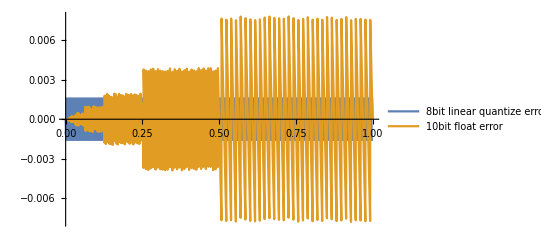

```mathematica
(*Visualize error of 10bit float vs 8bit linear RGB value*)
Plot[{eightBit[x]-x,fromReal32Digits[binaryRound[real32Digits[x],18]]-x},{x,0,1},PlotLegends->{"8bit linear quantize error","10bit float error"}]
```

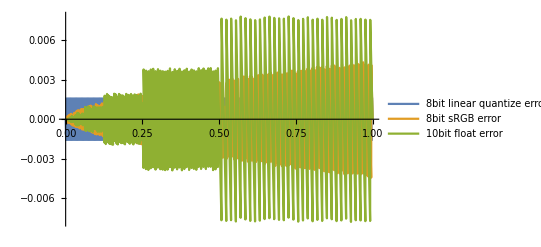

```mathematica
(*Visualize error of 10bit float vs 8bit linear RGB value vs 8bit sRGB*)
Plot[{eightBit[x]-x,eightBitSrgb[x]-x,fromReal32Digits[binaryRound[real32Digits[x],18]]-x},{x,0,1},PlotLegends->{"8bit linear quantize error","8bit sRGB error", "10bit float error"}]
```

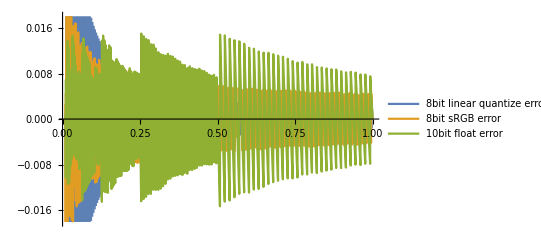

```mathematica
(*Visualize relative error of 10bit float vs 8bit linear RGB value vs 8bit sRGB*)
Plot[{(eightBit[x]-x)/x,(eightBitSrgb[x]-x)/x,(fromReal32Digits[binaryRound[real32Digits[x],18]]-x)/x},{x,0.01,1},PlotLegends->{"8bit linear quantize error","8bit sRGB error", "10bit float error"}]
```

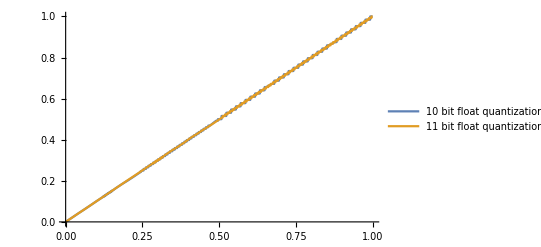

```mathematica
(*Compare 11 float to 10 float*)
Plot[{fromReal32Digits[binaryRound[real32Digits[x],18]],fromReal32Digits[binaryRound[real32Digits[x],17]]},{x,0.0,1.0},PlotLegends->{"10 bit float quantization","11 bit float quantization"}]
```

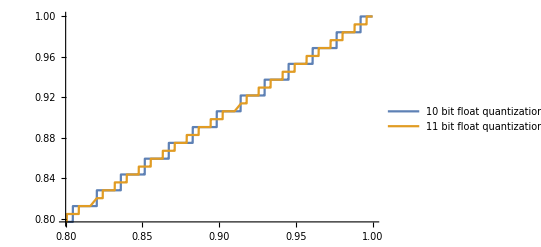

```mathematica
(*Compare 11 float to 10 float, range 0.8-1.0*)
Plot[{fromReal32Digits[binaryRound[real32Digits[x],18]],fromReal32Digits[binaryRound[real32Digits[x],17]]},{x,0.8,1.0},PlotLegends->{"10 bit float quantization","11 bit float quantization"}]
```

```mathematica
(*Show image with R11G11B10F gradient*)
Image[Transpose[Table[Module[{q11 = fromReal32Digits[binaryRound[real32Digits[x],17]],q10=fromReal32Digits[binaryRound[real32Digits[x],18]]},Table[{q11,q11,q10},{col,1,128}]],{x,0.5,0.6,0.0002}]],ColorSpace->"RGB"]
```

-Graphics-

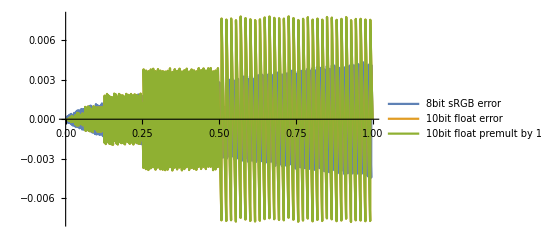

```mathematica
(*Show that premultiplying is not going to help with quantization error*)
Plot[{eightBitSrgb[x]-x,fromReal32Digits[binaryRound[real32Digits[x],18]]-x,fromReal32Digits[binaryRound[real32Digits[x*16],18]]/16-x},{x,0,1},PlotLegends->{"8bit sRGB error", "10bit float error","10bit float premult by 16 error"}]
```

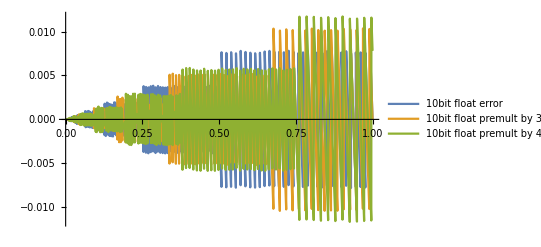

```mathematica
Plot[{fromReal32Digits[binaryRound[real32Digits[x],18]]-x,fromReal32Digits[binaryRound[real32Digits[x*3/4],18]]*4/3-x,fromReal32Digits[binaryRound[real32Digits[x*4/3],18]]*3/4-x},{x,0,1},PlotLegends->{ "10bit float error","10bit float premult by 3/4 error","10bit float premult by 4/3 error"}]
```

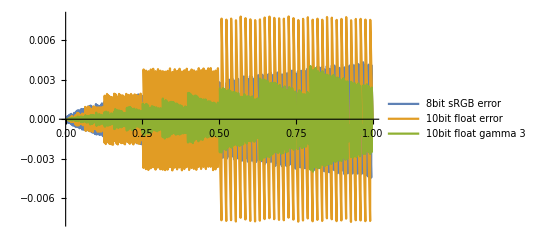

```mathematica
(*Apply a gamma function*)
Plot[{eightBitSrgb[x]-x,fromReal32Digits[binaryRound[real32Digits[x],18]]-x,Power[fromReal32Digits[binaryRound[real32Digits[x*x*x],18]],1/3]-x},{x,0,1},PlotLegends->{"8bit sRGB error", "10bit float error","10bit float gamma 3"}]
```

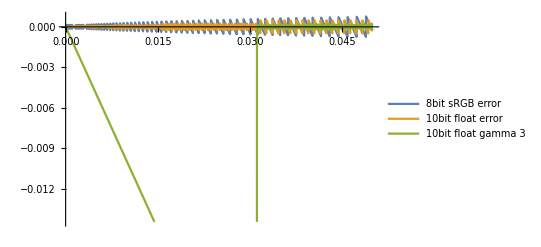

```mathematica
(*Actual zoomed in error *)
Plot[{eightBitSrgb[x]-x,fromReal32Digits[binaryRound[real32Digits[x],18]]-x,Power[Module[{y=fromReal32Digits[binaryRound[real32Digits[x*x*x],18]]},If[y<1/32768,0,y]],1/3]-x},{x,0,0.05},PlotLegends->{"8bit sRGB error", "10bit float error","10bit float gamma 3"}]
```

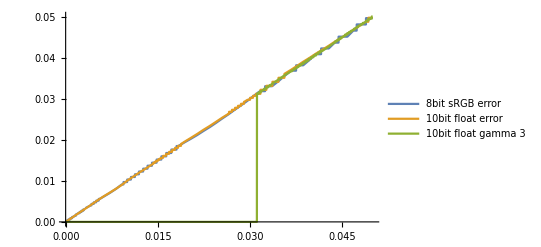

```mathematica
(*How the signal actually clips*)
Plot[{eightBitSrgb[x],fromReal32Digits[binaryRound[real32Digits[x],18]],Power[Module[{y=fromReal32Digits[binaryRound[real32Digits[x*x*x],18]]},If[y<1/32768,0,y]],1/3]},{x,0,0.05},PlotLegends->{"8bit sRGB error", "10bit float error","10bit float gamma 3"}]
```

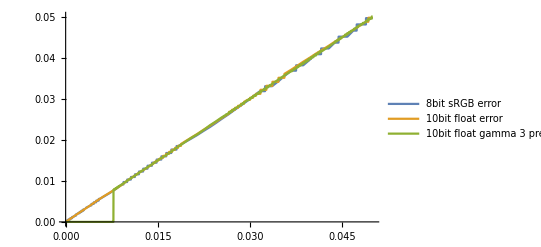

```mathematica
(*Improving it a bit with preexposing by 4*)
Plot[{eightBitSrgb[x],fromReal32Digits[binaryRound[real32Digits[x],18]],Power[Module[{y=fromReal32Digits[binaryRound[real32Digits[Power[4*x,3]],18]]},If[y<1/32768,0,y]],1/3]/4},{x,0,0.05},PlotLegends->{"8bit sRGB error", "10bit float error","10bit float gamma 3 preexposed"}]
```

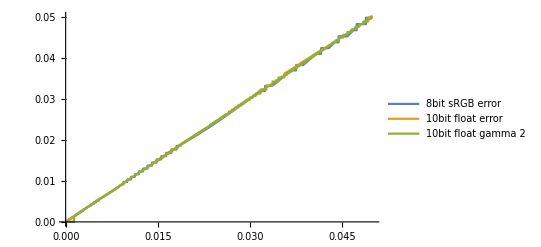

```mathematica
(*Alternative: just use gamma 2!*)
Plot[{eightBitSrgb[x],fromReal32Digits[binaryRound[real32Digits[x],18]],Power[Module[{y=fromReal32Digits[binaryRound[real32Digits[Power[4*x,2]],18]]},If[y<1/32768,0,y]],1/2]/4},{x,0,0.05},PlotLegends->{"8bit sRGB error", "10bit float error","10bit float gamma 2"}]
```

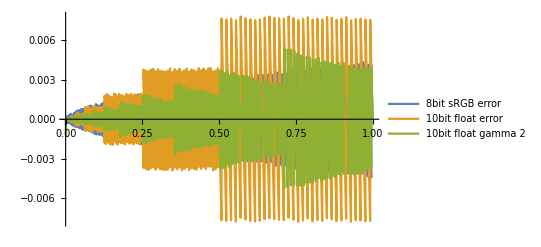

```mathematica
(*Error with gamma 2, not great, but not too bad*)
Plot[{eightBitSrgb[x]-x,fromReal32Digits[binaryRound[real32Digits[x],18]]-x,Power[Module[{y=fromReal32Digits[binaryRound[real32Digits[Power[4*x,2]],18]]},If[y<1/32768,0,y]],1/2]/4-x},{x,0,1.0},PlotLegends->{"8bit sRGB error", "10bit float error","10bit float gamma 2"}]
```